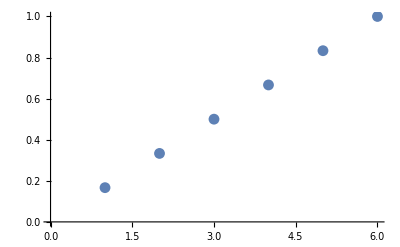

```mathematica
ListPlot[
{Table[{x, x 1/6}, {x,1,6}]}, 
DataRange->{0,4}]
```

```mathematica
1/3 π^2 + ∑_(n=1)^5 (-1)^n (4 Cos[n x])/n^2
```

π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]

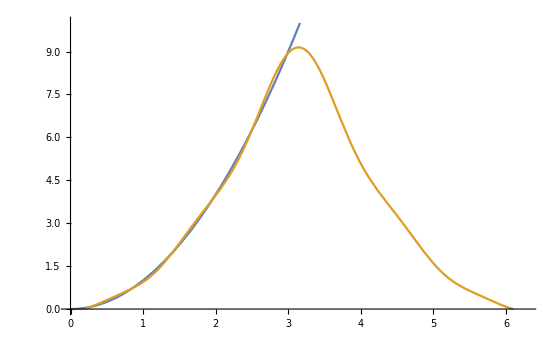

```mathematica
Plot[{x^2, 1/3 π^2 + ∑_(n=1)^5 (-1)^n (4 Cos[n x])/n^2}, {x,0,2π}, PlotRange->{0, 10}]
```

```mathematica
ExpandAll[1/π∫_-π^π x^3 Sin[n x]ⅆx]
```

(12 Cos[n π])/n^3-(2 π^2 Cos[n π])/n-(12 Sin[n π])/(n^4 π)+(6 π Sin[n π])/n^2

```mathematica
∫_-π^π x^3 ⅆx
```

0

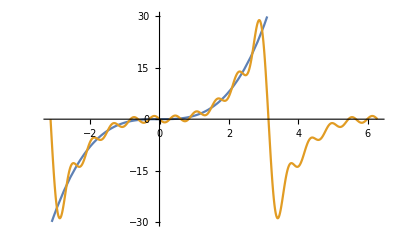

```mathematica
Plot[{x^3, ∑_(n=1)^10 (-1)^n((12 - 2 π^2 n^2)/n^3)Sin[n x]}, {x, -π, 2π}, PlotRange-> {-30, 30}]
```

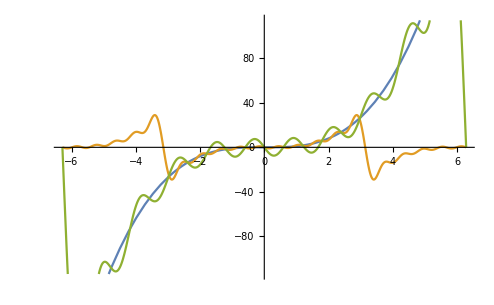

```mathematica
Plot[{x^3,∑_(n=1)^10 (-1)^n((12 - 2 π^2 n^2)/n^3)Sin[n x], 16∑_(n=1)^10 (-1)^n((6 - π^2 n^2)/n^3)Sin[(n x)/2]}, {x, -2π, 2π} ]
```

```mathematica
ExpandAll[1/(2π)∫_0^(2π) x^3 Sin[(n x)/2]ⅆx]
```

(48 Cos[n π])/n^3-(8 π^2 Cos[n π])/n-(48 Sin[n π])/(n^4 π)+(24 π Sin[n π])/n^2

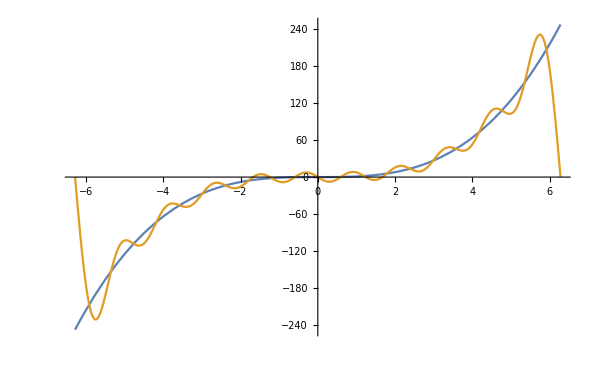

```mathematica
Plot[{x^3,16∑_(n=1)^10 (-1)^n((6 - π^2 n^2)/n^3)Sin[(n x)/2]},

 {x, -2π, 2π} ]
```

```mathematica
Animate[Plot[{x^2,1/3 π^2 + 4∑_(n=1)^5 (-1)^n(Cos[3 n t]Cos[n x])/n^2}, {x, 0, 2π}, PlotRange->{0, 10}], {t, 0, 2π}, 
AnimationRunning-> False]
```